# Examen 2: Parte Computacional Sistemas Dinámicos No Lineales

## Profesor: Josué Manik Nava Sedeño Alumno: Wei Le Hu Tang 24 de marzo del 2024

Elabora un notebook en el software mathemática respondiendo TODAS las preguntas. Para cada inciso interpreta lo que se esté analizando y escribelo en lenguaje natural. Dicha interpretación representa la MITAD del porcentaje de la calificación. (NO se contará ninguna interpretación sin argumento matemático y/o computacional)

## 1. Considera el sistema

### (a) Para cada podemos obtener un diagrama de bifurcación. Grafica todos los diagramas de bifurcación cualitativamente distintos para todo los casos en .

Analicemos las soluciones del sistema, cuando 



Entonces se tiene que el caso trivial  siempre va a ser solución independientemente de los parámetros

Veamos ahora la otra igualdad:




La solución real existe si el discriminante es no negativo, tal que por tricotomía:

Caso 1: 
	
	No hay solución real, porque no existe raiz real de un número negativo.
	Entonces sólo existe la solución trivial.
	
Caso 2: 
	
	Existe una única solución, aparte de la trivial, que es
	
	
	En total son dos soluciones, excepto si 

Caso 3: 
	
	Existen dos soluciones
	
	
	Habiendo tres soluciones en total, contando la trivial

Por lo tanto  es un punto de bifurcación

Llegamos a que existen a lo más tres soluciones, que son:


Nótese que, por la naturaleza del polinomio de tercer grado que define a , como el término cúbico tiene coeficiente negativo:
 lo que implica que la primera solución o bien  es siempre al menos estable por la izquierda, porque  pasa que 
Análogamente, el punto de equilibrio más grande  es al menos estable por la derecha
Véase esto en la siguiente gráfica interactiva de

```mathematica
M=20;
Manipulate[Plot[r x+a x^2-x^3,{x,-8,8},AxesLabel->{"x","x*"}],{a,-M,M},{r,-M,M}]
```

```mathematica
(*Soluciones x1 y x2 del sistema y punto de bifurcación*)
x1[r_,a_]=(a-Sqrt[a^2+4r])/2;
x2[r_,a_]=(a+Sqrt[a^2+4r])/2;
bif[a_]=-a^2/4;
```

#### Sea

Entonces el punto de bifurcación está en 
Analicemos qué pasa antes durante y después de este momento

Si  
	
	
	
Si 
	
	
	En estos dos casos, como  es la única solución de equilibrio, entonces , y por el análisis anterior, es un punto de equilibrio estable
	
Si 
	
	
	Entonces la ecuación puede escribirse como 
	Más aun: 
	
	 es estable por la izquierda y  estable por la derecha
	Como  es un polinomio cúbico negativo, y  es el conjunto de sus raíces
	, entonces  es estable por la derecha y  inestable por la izquierda
	, entonces  es estable por la izquierda y  inestable por la derecha
	 son estables y  inestable

Por lo tanto  es un punto de bifurcación de tipo tridente supercrítico

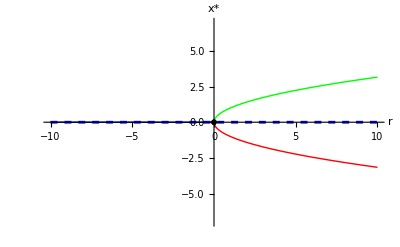

```mathematica
With[{a=0},Show[
Plot[0,{r,-10,10},PlotStyle->{Blue,Dashed}, PlotRange->{{-10,10},{-7,7}},AxesLabel->{"r","x*"}],
Plot[0,{r,-10,0},PlotStyle->{Blue, Thick}],
Plot[Evaluate@{If[x1[r,a]>0,x1[r,a]],If[x1[r,a]<=0,x1[r,a]]},{r,bif[a],10},PlotStyle->{{Red, Dashed},{Red,Thick}}],
Plot[Evaluate@{If[x2[r,a]<0,x2[r,a]],If[x2[r,a]>=0,x2[r,a]]},{r,bif[a],10},PlotStyle->{{Green, Dashed},{Green,Thick}}],
ListPlot[{{{bif[a],x1[bif[a],a]}},{{0,0}}},PlotMarkers->{★,●},PlotStyle->{Black,Black}]
]]
```

#### Sea

Entonces existe un punto de bifurcación cuando 

Si 
	
	
	
	Sólo existe la solución trivial que es estable

Si 
	
	 entonces esta raiz del polinomio tiene multiplicidad 2
	
	Entonces la ecuación puede escribirse como 
	Más aun, como 
	
	 es estable por la izquierda y  estable por la derecha
	Por la multiplicidad de  y el comportamiento del polinomio
	
	 es estable por la derecha y  es inestable por la izquierda
	 es estable y  es semiestable por la derecha

Si 
	
	
	Nótese que son diferentes puntos exceptos en 
	, entonces 
	
	Si 
		
		Por el comportamiento del polinomio:
		 es estable  es inestable, y  es estable
		Por lo tanto  es un punto de bifurcación de tipo nodo silla para 

	Si 
		
		Por el comportamiento del polinomio:
		 es estable,  es inestable, y  es estable
		Por lo tanto  es un punto de bifurcación de tipo transcrito para  porque cambia sus estabilidades

Véase en particular la gráfica para

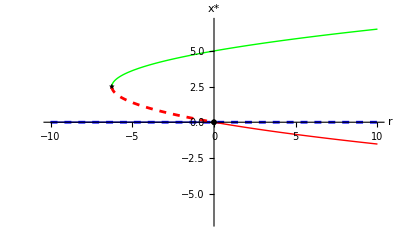

```mathematica
With[{a=5},Show[
Plot[0,{r,-10,10},PlotStyle->{Blue,Dashed}, PlotRange->{{-10,10},{-7,7}},AxesLabel->{"r","x*"}],
Plot[0,{r,-10,0},PlotStyle->{Blue, Thick}],
Plot[Evaluate@{If[x1[r,a]>0,x1[r,a]],If[x1[r,a]<=0,x1[r,a]]},{r,bif[a],10},PlotStyle->{{Red, Dashed},{Red,Thick}}],
Plot[Evaluate@{If[x2[r,a]<0,x2[r,a]],If[x2[r,a]>=0,x2[r,a]]},{r,bif[a],10},PlotStyle->{{Green, Dashed},{Green,Thick}}],
ListPlot[{{{bif[a],x1[bif[a],a]}},{{0,0}}},PlotMarkers->{★,●},PlotStyle->{Black,Black}]
]]
```

#### Sea

Por un análisis completamente análogo al anterior, por la simetría de :
Si 
	
	0 es el único punto de equilibrio y es estable

Si 
	
	Donde 
	 es estable y  es semiestable por la izquierda

Si 
	Si 
		
		 es estable,  es inestable, y  es estable
		Por lo tanto  es un punto de bifurcación de tipo nodo silla para 
	Si 
		
		 es estable,  es inestable, y  es estable
		Por lo tanto  es un punto de bifurcación de tipo transcrito para  porque cambia sus estabilidades
	
Véase en particular la gráfica para

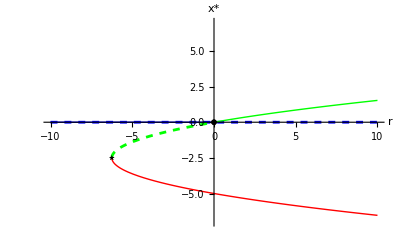

```mathematica
With[{a=-5},Show[
Plot[0,{r,-10,10},PlotStyle->{Blue,Dashed}, PlotRange->{{-10,10},{-7,7}},AxesLabel->{"r","x*"}],
Plot[0,{r,-10,0},PlotStyle->{Blue, Thick}],
Plot[Evaluate@{If[x1[r,a]>0,x1[r,a]],If[x1[r,a]<=0,x1[r,a]]},{r,bif[a],10},PlotStyle->{{Red, Dashed},{Red,Thick}}],
Plot[Evaluate@{If[x2[r,a]<0,x2[r,a]],If[x2[r,a]>=0,x2[r,a]]},{r,bif[a],10},PlotStyle->{{Green, Dashed},{Green,Thick}}],
ListPlot[{{{bif[a],x1[bif[a],a]}},{{0,0}}},PlotMarkers->{★,●},PlotStyle->{Black,Black}]
]]
```

#### Gráfica interactiva de bifurcación dado

```mathematica
Manipulate[
Show[
Plot[0,{r,-10,10},PlotStyle->{Blue,Dashed}, PlotRange->{{-10,10},{-7,7}},AxesLabel->{"r","x*"}],
Plot[0,{r,-10,0},PlotStyle->{Blue, Thick}],
Plot[Evaluate@{If[x1[r,a]>0,x1[r,a]],If[x1[r,a]<=0,x1[r,a]]},{r,bif[a],10},PlotStyle->{{Red, Dashed},{Red,Thick}}],
Plot[Evaluate@{If[x2[r,a]<0,x2[r,a]],If[x2[r,a]>=0,x2[r,a]]},{r,bif[a],10},PlotStyle->{{Green, Dashed},{Green,Thick}}],
ListPlot[{{{bif[a],x1[bif[a],a]}},{{0,0}}},PlotMarkers->{★,●},PlotStyle->{Black,Black}]
],
{a,-5,5}]
```

### (b) Grafica el plano e identifica los tipos de bifurcación que hay.

Retomando el inciso anterior, se sabe que
Si 
	 es un punto de bifurcación transcrito
	 es una bifurcación de nodo silla
Si 
	Los dos casos se vuelven el mismo, volviendo a  una bifurcación de tridente supercrítico

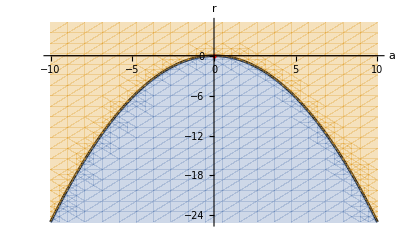

```mathematica
r[a_]=-a^2/4;
Show[
Plot[r[a],{a,-10,10},
PlotStyle->{Black},
PlotRange->{{-10,10},{-25,5}},
AxesLabel->{"a","r"}],
RegionPlot[{r < -a^2/4,r > -a^2/4},{a,-10,10},{r,-25,5},BoundaryStyle->None],
Epilog->{{Brown,Thick,Line[{{-10,0},{10,0}}]},{Red,PointSize@Large,Point[{0,0}]}}
]
```

La región azul    sólo cuenta con la solución trivial 
La región amarilla    cuenta con tres soluciones diferentes
La linea negra    es la bifurcación de punto silla, sobre la cual existen dos soluciones pues 
La linea café    es la bifurcación transcrita donde  se cruza con  o 
En el punto  se encuentra la bifurcación de tipo tridente supercrítica

## 2. Considera el modelo de recolección adimensionalizado visto en el exámen teórico

### (a) Grafica el plano e identifica los tipos de bifurcación que hay.

Nótese entonces que:


Que es una expresión del tipo del modelo del ejercicio anterior
Lo que era  ahora es  y lo que era  ahora es 

Tal que:
Si , equivalente a 
	 es un punto de bifurcación transcrito
	 es una bifurcación de nodo silla
Si , equivalente a 
	Los dos casos se vuelven el mismo, volviendo a  una bifurcación de tridente supercrítico

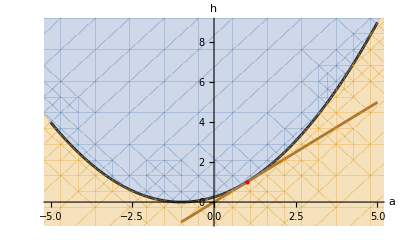

```mathematica
h[a_]=(a+1)^2/4;
Show[
Plot[{h[a],a},{a,-5,5},
Epilog->{Red,PointSize@Large,Point[{1,1}]},
PlotStyle->{Black,Brown},
PlotRange->{{-5,5},{-1,9}},
AxesLabel->{"a","h"}],
RegionPlot[{h>(a+1)^2/4,h<(a+1)^2/4},{a,-11,9},{h,-5,25},BoundaryStyle->None]
]
```

La región azul    sólo cuenta con la solución trivial 
La región amarilla    cuenta con tres soluciones diferentes
La linea negra    es la bifurcación de punto silla, sobre la cual existen dos soluciones pues 
La linea café    es la bifurcación transcrita donde  se cruza con  o 
En el punto  se encuentra la bifurcación de tipo tridente supercrítica

### (b) Grafica el espacio . Investiga que es la histéresis y comenta si existe en este modelo.

```mathematica
Plot3D[{0,x1[a-h,1-a],x2[a-h,1-a]},{a,-10,10},{h,-10,10},PlotStyle->{Blue,Red,Green},AxesLabel->{"a","h","x*"}]
```

-Graphics3D-

Según la Universidad Complutense de Madrid: “la histéresis es la tendencia de un material a conservar una de sus propiedades en ausencia del estímulo que la ha generado.”

Sí hay histéresis en el sistema, porque intuitivamente, tómese la gráfica de bifurcación de

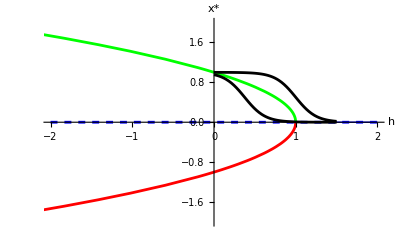

```mathematica
With[{a=1},Show[
Plot[0,{h,-2,2},AxesLabel->{"h","x*"},PlotStyle->{Blue,Dashed},PlotRange->{-2,2}],
Plot[0,{h,1,2},PlotStyle->{Blue,Thick}],
Plot[{x1[a-h,1-a],x2[a-h,1-a]},{h,-10,10},PlotStyle->{Red,Green}],
Plot[1/(1+Exp[8h-3]),{h,0,1.5},PlotStyle->{Black}],
Plot[1/(1+Exp[8h-8]),{h,0,1.5},PlotStyle->{Black}]
]]
```

Supongamos que esta gráfica modela una propiedad  de algun material, dado un factor  que se va deteriorando con el tiempo, tal que  es ideal.
Entonces suponiendo que h>1 que es el punto de bifurcación, y la región donde el estado del material es estable; y  con  suficientemente chico.
Conforme pase el tiempo,  va disminuyendo hasta que llega a ser menor que , inestabilizando y haciendo tender  a la linea verde (o roja en caso de .
Entonces se somete un estímulo para modificar el factor  hasta que vuelva a ser mayor que 1, y el material pueda volver a tender a .
El ciclo formado por este proceso (trazado de negro) se le conoce como histéresis.

## 3. For each of the following questions, draw the phase portrait as function of the control parameter . Classify the bifurcations that occur as varies, and find all the bifurcation values of .

### 4.3.3

```mathematica
Manipulate[Plot[mu Sin[theta]-Sin[2 theta],{theta,-10,10}],{mu,-10,10}]
```

### 4.3.4

```mathematica
Manipulate[Plot[Sin[theta]/(mu + Cos[theta]),{theta,-10,10}],{mu,-10,10}]
```

### 4.3.7

```mathematica
Manipulate[Plot[Sin[theta]/(mu + Sin[theta]),{theta,-10,10}],{mu,-10,10}]
```